```mathematica
$LoadAddOns={"FeynHelpers"};
$LoadFeynArts=True;
<<FeynCalc`
$FAVerbose=False;
```

FeynCalc 9.2.0. For help, use the documentation center, check out the wiki or write to the mailing list.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207C, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

FeynArts 3.9 patched for use with FeynCalc, for documentation use the manual or visit www.feynarts.de.

FeynHelpers 1.0.0 loaded.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", TUM-EFT 75/15, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
$KeepLogDivergentScalelessIntegrals=True;
```

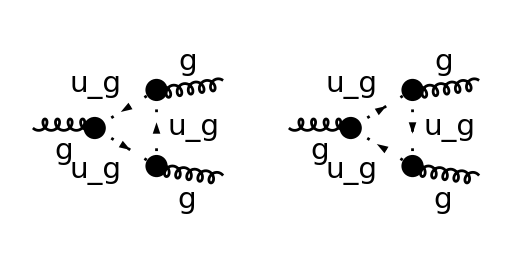

```mathematica
top=CreateTopologies[1,1->2,ExcludeTopologies->{WFCorrections,SelfEnergies,Tadpoles}];
diags=InsertFields[top,{V[5]}->{V[5],V[5]},Model->"SMQCD",InsertionLevel -> {Particles},ExcludeParticles->{F[__],S[_],V[_],U[1|2|3|4]}];
Paint[diags, ColumnsXRows -> {2, 1},SheetHeader -> False,SheetHeader->None,Numbering -> None,ImageSize->{512,256}];
```

```mathematica
amps=FCFAConvert[CreateFeynAmp[diags, Truncated -> True,GaugeRules->{},PreFactor->1],IncomingMomenta->{p1},
OutgoingMomenta->{p2,p3},LoopMomenta->{q},DropSumOver->True,UndoChiralSplittings->True,ChangeDimension->D,List->True,SMP->True,LorentzIndexNames->{λ,μ,ν},
SUNIndexNames->{a,b,c}]//Contract//SUNSimplify
```

{(ⅈ C_A g_s^3 q^μ (q-p2)^ν f^abc (-p2-p3+q)^λ)/(2 q^2.(q-p2)^2.(-p2-p3+q)^2),(ⅈ C_A g_s^3 q^λ (p2-q)^μ f^abc (p2+p3-q)^ν)/(2 q^2.(q-p2)^2.(-p2-p3+q)^2)}

```mathematica
amps2=amps[[2]]/.p3->-p2/.p2->p
```

-(ⅈ C_A g_s^3 q^λ q^ν (p-q)^μ f^abc)/(2 q^2.(q-p)^2.q^2)

```mathematica
amps1=amps[[1]]/.p3->-p2/.p2->p
```

(ⅈ C_A g_s^3 q^λ q^μ (q-p)^ν f^abc)/(2 q^2.(q-p)^2.q^2)

```mathematica
xxx=TID[amps1+amps2,q,ToPaVe->True]
```

(π^2 C_A g_s^3 p^λ B_0(0,0,0) f^abc (2 D p^μ p^ν-(D+2) p^μ p^ν+p^2 g^μν))/(8 (1-D) p^2)-(π^2 C_A g_s^3 B_0(p^2,0,0) f^abc (4 D p^λ p^μ p^ν-3 (D+2) p^λ p^μ p^ν+p^2 p^ν g^λμ-p^2 p^λ g^μν+p^2 p^μ g^λν+4 p^λ p^μ p^ν))/(8 (1-D) p^2)-(π^2 C_A g_s^3 p^λ C_0(0,p^2,p^2,0,0,0) f^abc (2 D p^μ p^ν-(D+2) p^μ p^ν+p^2 g^μν))/(8 (1-D))

```mathematica
xxx[[1]]//PaXEvaluateUVIRSplit[#,q]&
xxx[[2]]//PaXEvaluateUVIRSplit[#,q]&
xxx[[3]]//PaXEvaluateUVIRSplit[#,q]&
```

(π^2 C_A g_s^3 p^λ f^abc (-3 p^2 g^μν log(-μ^2/p^2)+3 ℽ p^2 g^μν-2 p^2 g^μν+3 p^2 log(π) g^μν-6 p^μ p^ν log(-μ^2/p^2)+6 ℽ p^μ p^ν+2 p^μ p^ν+6 log(π) p^μ p^ν))/(72 p^2)-(π^2 C_A g_s^3 p^λ f^abc (p^2 g^μν+2 p^μ p^ν))/(24 p^2 ε_IR)

(π^2 C_A g_s^3 p^λ f^abc (p^2 g^μν+2 p^μ p^ν))/(24 p^2 ε_IR)-(π^2 C_A g_s^3 p^λ g^μν f^abc)/(24 ε_UV)-(π^2 C_A g_s^3 p^λ p^μ p^ν f^abc)/(12 p^2 ε_UV)

-1/24 π^2 C_A g_s^3 p^λ g^μν log(-μ^2/p^2) f^abc+1/24 π^2 C_A g_s^3 p^μ g^λν log(-μ^2/p^2) f^abc+1/24 π^2 C_A g_s^3 p^ν g^λμ log(-μ^2/p^2) f^abc+(π^2 C_A g_s^3 p^λ p^μ p^ν log(-μ^2/p^2) f^abc)/(12 p^2)+1/72 π^2 (-8+3 ℽ+3 log(π)) C_A g_s^3 p^λ g^μν f^abc-1/72 π^2 (-8+3 ℽ+3 log(π)) C_A g_s^3 p^μ g^λν f^abc-1/72 π^2 (-8+3 ℽ+3 log(π)) C_A g_s^3 p^ν g^λμ f^abc-(π^2 (-5+3 ℽ+3 log(π)) C_A g_s^3 p^λ p^μ p^ν f^abc)/(36 p^2)-(π^2 C_A g_s^3 p^λ g^μν f^abc)/(24 ε_UV)+(π^2 C_A g_s^3 p^μ g^λν f^abc)/(24 ε_UV)+(π^2 C_A g_s^3 p^ν g^λμ f^abc)/(24 ε_UV)+(π^2 C_A g_s^3 p^λ p^μ p^ν f^abc)/(12 p^2 ε_UV)

```mathematica
res=PaXEvaluateUVIRSplit[xxx,q]
```

-1/12 π^2 C_A g_s^3 p^λ g^μν log(-μ^2/p^2) f^abc+1/24 π^2 C_A g_s^3 p^μ g^λν log(-μ^2/p^2) f^abc+1/24 π^2 C_A g_s^3 p^ν g^λμ log(-μ^2/p^2) f^abc+(π^2 C_A g_s^3 p^λ p^μ p^ν f^abc)/(6 p^2)+1/36 π^2 (-5+3 ℽ+3 log(π)) C_A g_s^3 p^λ g^μν f^abc-1/72 π^2 (-8+3 ℽ+3 log(π)) C_A g_s^3 p^μ g^λν f^abc-1/72 π^2 (-8+3 ℽ+3 log(π)) C_A g_s^3 p^ν g^λμ f^abc-(π^2 C_A g_s^3 p^λ g^μν f^abc)/(12 ε_UV)+(π^2 C_A g_s^3 p^μ g^λν f^abc)/(24 ε_UV)+(π^2 C_A g_s^3 p^ν g^λμ f^abc)/(24 ε_UV)

```mathematica
res//FCHideEpsilon
```

1/(72 p^2)π^2 C_A g_s^3 f^abc (3 p^2 p^ν g^λμ log(-μ^2/p^2)-6 p^2 p^λ g^μν log(-μ^2/p^2)+3 p^2 p^μ g^λν log(-μ^2/p^2)+8 p^2 p^ν g^λμ-10 p^2 p^λ g^μν+8 p^2 p^μ g^λν-3 p^2 log(4 π) p^ν g^λμ-3 p^2 log(π) p^ν g^λμ+6 p^2 log(4 π) p^λ g^μν+6 p^2 log(π) p^λ g^μν-3 p^2 log(4 π) p^μ g^λν-3 p^2 log(π) p^μ g^λν+12 p^λ p^μ p^ν)-1/24 π^2 C_A g_s^3 Δ_UV f^abc (2 p^λ g^μν-p^μ g^λν-p^ν g^λμ)